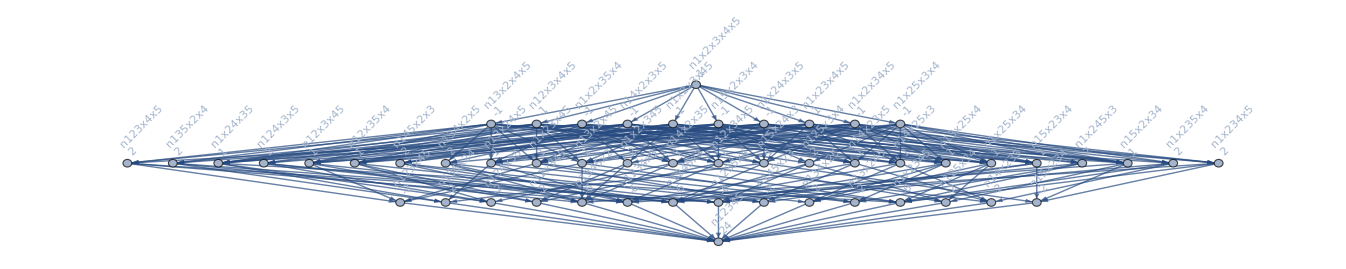

```mathematica
m=MobiusGraph[k5Key]
```

```mathematica
step1=Select[EdgeList [m],#[[2]]==n13x24x5&]
```

{n13x2x4x5->n13x24x5,n15x2x3x4->n13x24x5,n1x24x3x5->n13x24x5,n1x25x3x4->n13x24x5,n1x2x35x4->n13x24x5,n1x2x3x45->n13x24x5}

```mathematica
step1b=Map[First,step1]//DeleteDuplicates
```

{n13x2x4x5,n15x2x3x4,n1x24x3x5,n1x25x3x4,n1x2x35x4,n1x2x3x45}

```mathematica
step2=Select[EdgeList [m],MemberQ[step1b,#[[2]]]&]//DeleteDuplicates
```

{n1x2x3x4x5->n13x2x4x5,n1x2x3x4x5->n15x2x3x4,n1x2x3x4x5->n1x24x3x5,n1x2x3x4x5->n1x25x3x4,n1x2x3x4x5->n1x2x35x4,n1x2x3x4x5->n1x2x3x45}

```mathematica
step2b=Map[First,step2]
```

{n1x2x3x4x5,n1x2x3x4x5,n1x2x3x4x5,n1x2x3x4x5,n1x2x3x4x5,n1x2x3x4x5}

```mathematica
MobiusA[n12345,n1x2x3x4x5]
```

24

```mathematica
step3=Select[EdgeList [m],MemberQ[step2b,#[[2]]]&]
```

{}

```mathematica
Table[MobiusA[k,n1x2x3x4x5]*k,{k,{n13x24x5,n13x2x4x5,n15x2x3x4,n1x24x3x5,n1x25x3x4,n1x2x35x4,n1x2x3x45,n1x2x3x4x5}}]
```

{n13x24x5,-n13x2x4x5,-n15x2x3x4,-n1x24x3x5,-n1x25x3x4,-n1x2x35x4,-n1x2x3x45,n1x2x3x4x5}

```mathematica
(Table[MobiusA[k,n1x2x3x4x5]*k,{k,{n13x24x5,n13x2x4x5,n15x2x3x4,n1x24x3x5,n1x25x3x4,n1x2x35x4,n1x2x3x45,n1x2x3x4x5}}]//Total)/.repRealDemo
```

-2106

```mathematica
MobiusA[n13x24x5,n13x24x5]n13x24x5+(n13x2x4x5+n15x2x3x4+n1x24x3x5+n1x25x3x4+n1x2x35x4+n1x2x3x45)-n1x2x3x4x5/.repRealDemo
```

2106

```mathematica
allGraphs[alfa1Key,"colofourrealnull"]/.repRealDemo
```

58

```mathematica
step1=Select[EdgeList [m],#[[2]]==n14x23x5&]
```

{n14x2x3x5->n14x23x5,n15x2x3x4->n14x23x5,n1x23x4x5->n14x23x5,n1x25x3x4->n14x23x5,n1x2x35x4->n14x23x5,n1x2x3x45->n14x23x5}

```mathematica
step1b=Map[First,step1]//DeleteDuplicates
```

{n14x2x3x5,n15x2x3x4,n1x23x4x5,n1x25x3x4,n1x2x35x4,n1x2x3x45}

```mathematica
step2=Select[EdgeList [m],MemberQ[step1b,#[[2]]]&]//DeleteDuplicates
```

{n1x2x3x4x5->n14x2x3x5,n1x2x3x4x5->n15x2x3x4,n1x2x3x4x5->n1x23x4x5,n1x2x3x4x5->n1x25x3x4,n1x2x3x4x5->n1x2x35x4,n1x2x3x4x5->n1x2x3x45}

```mathematica
step2b=Map[First,step2]
```

{n1x2x3x4x5,n1x2x3x4x5,n1x2x3x4x5,n1x2x3x4x5,n1x2x3x4x5,n1x2x3x4x5}

```mathematica
step3=Select[EdgeList [m],MemberQ[step2b,#[[2]]]&]
```

{}

```mathematica
(-n14x23x5+n14x2x3x5+n15x2x3x4+n1x23x4x5+n1x25x3x4+n1x2x35x4+n1x2x3x45-n1x2x3x4x5/.repRealDemo)
```

2474

```mathematica
allGraphs[quad1Key,"colofourrealnull"]/.repRealDemo
```

72

```mathematica
allGraphs[beta1Key,"colofourrealnull"]/.repRealDemo
```

52

```mathematica
SetP[4]
```

{Posets`Private`SetRefine,{{1,2,3,4}},3}

```mathematica
Build[SetP[8],sub4]
```

Building poset sub4  ...

Done

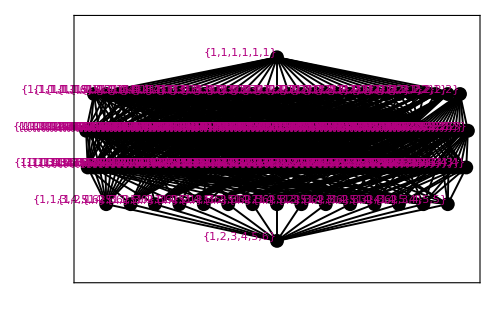

```mathematica
Diagram[sub4,ShowLabels->{1}]
```

```mathematica
ZetaPoly[sub4,x]
```

-(2 x)/3+5 x^2-(65 x^3)/6+(15 x^4)/2

```mathematica
MakeOne2[mat_]:=Map[Map[If[#!=0,1,0]&,#]&, mat]
```

```mathematica
BellB[8]
```

4140

```mathematica
Build[SetP[2],sub4]
```

Building poset sub4  ...

Done

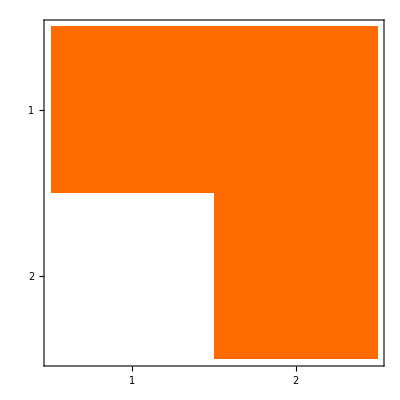

```mathematica
MakeOne2[ZetaP[sub4]]//MatrixPlot
```

Building poset sub4  ...

Done

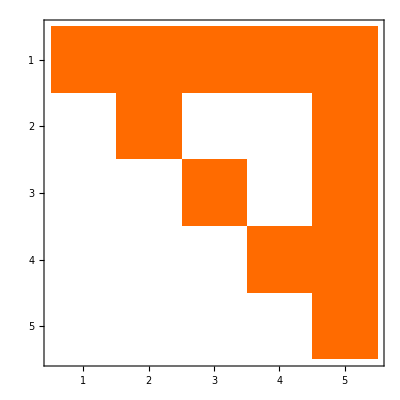

```mathematica
Build[SetP[3],sub4];MakeOne2[ZetaP[sub4]]//MatrixPlot
```

Building poset sub4  ...

Done

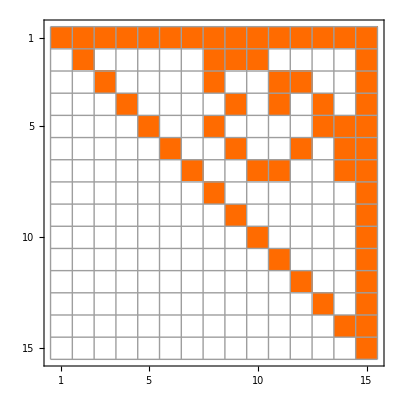

```mathematica
Build[SetP[4],sub4];MatrixPlot[MakeOne2[ZetaP[sub4]],Mesh->All]
```

Building poset sub4  ...

Done

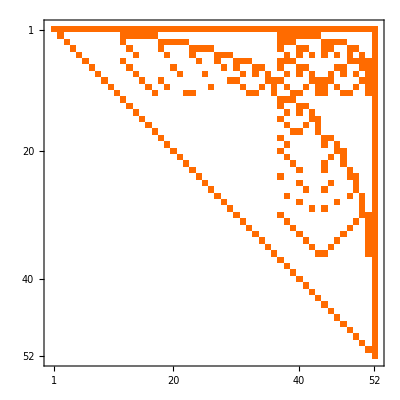

```mathematica
Build[SetP[5],sub4];MakeOne2[ZetaP[sub4]]//MatrixPlot
```

Building poset sub4  ...

Done

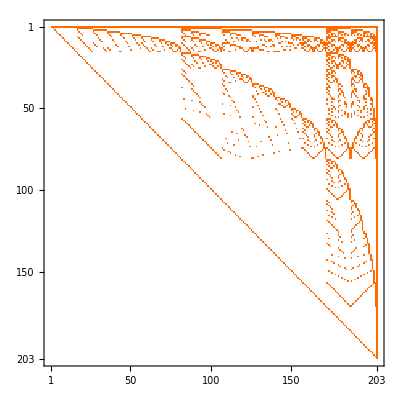

```mathematica
Build[SetP[6],sub4];MakeOne2[ZetaP[sub4]]//MatrixPlot
```

```mathematica
Build[SetP[7],sub4];MakeOne2[ZetaP[sub4]]//MatrixPlot
```

Building poset sub4  ...

Done

-Graphics-

```mathematica
Build[SetP[8],sub4];MakeOne2[ZetaP[sub4]]//MatrixPlot
```

Building poset sub4  ...

Done

-Graphics-